# ϕ^3 in 4D

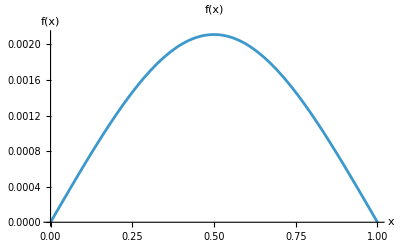

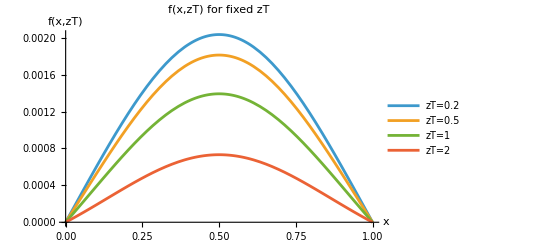

```mathematica
ClearAll[x,zT,g,m,u]

(*choose parameter values*)
g=1;
m=1;

u[x_]:=m^2 (x^2-x+1);

fZ[x_,zT_]:=(g^2/(16 Pi^2)) x (1-x) (zT/Sqrt[u[x]]) BesselK[1,zT Sqrt[u[x]]];

f[x_]:=(g^2/(16 m^2 Pi^2)) x (1-x)/(x^2-x+1);

(*Plot f(x)*)
Plot[f[x],{x,0,1},PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"f(x)"]

(*Plot f(x,zT) as a function of x for fixed zT values*)
Plot[Evaluate[Table[fZ[x,z],{z,{0.2,0.5,1,2}}]],{x,0,1},PlotRange->All,AxesLabel->{"x","f(x,zT)"},PlotLegends->{"zT=0.2","zT=0.5","zT=1","zT=2"},PlotLabel->"f(x,zT) for fixed zT"]
```

```mathematica
ClearAll[x,zT,g,m,u,fZ,f]

g=1;
m=1;

u[x_]:=m^2 (x^2-x+1);

fZ[x_,zT_]:=(g^2/(16 Pi^2)) x (1-x) (zT/Sqrt[u[x]]) BesselK[1,zT Sqrt[u[x]]];

f[x_]:=(g^2/(16 m^2 Pi^2)) x (1-x)/(x^2-x+1);

Manipulate[Plot[{f[x],fZ[x,zT]},{x,0,1},PlotRange->All,AxesLabel->{"x","f"},PlotLegends->{"f(x)","f(x,zT)"},PlotLabel->Row[{"Comparison at zT = ",zT}]],{zT,0.1,5}]
```

# ϕ^3 in 6D

0

20

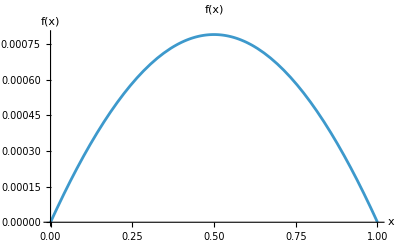

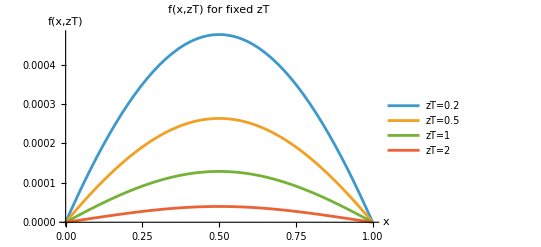

```mathematica
ClearAll[x,zT,g,m,u]

(*choose parameter values*)
g=1;
m=1;
DUV=0
mu=20

u[x_]:=m^2 (x^2-x+1);

fXMu[x_,mu_]:=(g^2/(4 Pi)^3) x (1-x) (DUV+Log[mu^2/u[x]]);

fXZ[x_,zT_]:=(g^2/(32 Pi^3)) x (1-x) BesselK[0,Sqrt[u[x] zT^2]];

(*Plot f(x)*)
Plot[f[x],{x,0,1},PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"f(x)"]

(*Plot f(x,zT) as a function of x for fixed zT values*)
Plot[Evaluate[Table[fZ[x,z],{z,{0.2,0.5,1,2}}]],{x,0,1},PlotRange->All,AxesLabel->{"x","f(x,zT)"},PlotLegends->{"zT=0.2","zT=0.5","zT=1","zT=2"},PlotLabel->"f(x,zT) for fixed zT"]
```

```mathematica
ClearAll[x,zT,g,mu,m,u,fXMu,fXZ]

g=1;
m=1;
DUV=0;

u[x_]:=m^2 (x^2-x+1);

fXMu[x_,mu_]:=(g^2/(4 Pi)^3) x (1-x) (DUV+Log[mu^2/u[x]]);

fXZ[x_,zT_]:=(g^2/(64 Pi^3)) x (1-x) BesselK[0,Sqrt[u[x] zT^2]];

Manipulate[Plot[{fXMu[x,mu],fXZ[x,zT]},{x,0,1},PlotRange->All,AxesLabel->{"x","f"},PlotLegends->{"f(x,μ)","f(x,zT)"},PlotLabel->Row[{"Comparison:  μ = ",mu,",  zT = ",zT}]],{zT,0.1,5},{mu,0.1,5}]
```

# SCALAR DIQUARK MODEL

```mathematica
ClearAll[x,zT,mu,g,m,M,DUV,u,fXMu,fXZ]

g=1;
m=1;
M=1;
DUV=0;

u[x_]:=m^2 (x^2-x+1);

fXMu[x_,mu_]:=g^2/(32 Pi^2) (1-x)*(DUV+Log[mu^2/u[x]]-1+(m+x M)^2/u[x]);

fXZ[x_,zT_]:=g^2/(32 Pi^2) (1-x)*(2 BesselK[0,Sqrt[u[x]] zT]+((m+x M)^2-u[x]) (zT/Sqrt[u[x]]) BesselK[1,Sqrt[u[x]] zT]);

Manipulate[Plot[{fXMu[x,mu],fXZ[x,zT]},{x,0.001,0.999},PlotRange->All,AxesLabel->{"x","f"},PlotLegends->{"f(x,μ)","f(x,z_T)"},PlotLabel->Row[{"μ = ",mu,",  z_T = ",zT}]],{zT,0.01,5},{mu,0.1,5}]
```

```mathematica
AXIAL  DIQUARK  MODEL
```

```mathematica
ClearAll[x,zT,g,mu,m,M,DUV,u,fXMu,fXZ]

g=1;
m=1;
M=1;
DUV=0;

u[x_]:=m^2 (x^2-x+1);

fXMu[x_,mu_]:=g^2/(8 Pi^2) (1+x^2)/(1-x)*(DUV+Log[mu^2/u[x]]-1+(1-x) (m+x M)^2/u[x]);

fXZ[x_,zT_]:=(g^2/(8 Pi^2) ((1+x^2)/(1-x))*(2 BesselK[0,Sqrt[u[x]] zT]-u[x] zT/Sqrt[u[x]] BesselK[1,Sqrt[u[x]] zT])+g^2/(8 Pi^2) (1-x) (m+x M)^2*(zT/Sqrt[u[x]]) BesselK[1,Sqrt[u[x]] zT]);

Manipulate[Plot[{fXMu[x,mu],fXZ[x,zT]},{x,0.001,0.95},PlotRange->{{0,1},{-0.5,1}},AxesLabel->{"x","f"},PlotLegends->{"f(x,μ)","f(x,z_T)"},PlotLabel->Row[{"μ = ",mu,",  z_T = ",zT}],PlotPoints->100,MaxRecursion->4],{zT,0.01,5},{mu,0.1,5}]
```